# Anonymous functions

## Comprehension Questions

Math 250 - Mathematical Computing
Christopher Hanusa

### 6-1. Use the command Function to define a function “firstLast” that takes as input a list and outputs the list consisting of the first element of the input and the last element of the input.

### 6-2. For each of the following anonymous functions, write a sentence describing what it does. Find a suitable input (or inputs) and verify that the function does what you think it should.

```mathematica
(#^3+(#-1)^2)&
```

f(x)=x^3+(x-1)^2

```mathematica
(#^3+(#-1)^2)&[11]
```

1431

```mathematica
11^3
```

1331

```mathematica
10^2
```

100

```mathematica
Range[Length[#]]&
```

```mathematica
Range[Length[#]]&[{3,4,72,14,312,123}]
```

{1,2,3,4,5,6}

```mathematica
#[[2]]&[{3,4,72,14,312,123}]
```

4

### 6-2.5 Create an anonymous function that will give the number plus one:

```mathematica
(#+1)&[15]
```

16

### 6-2.75 Create an anonymous function that gives a list that contains the number and the number plus one.

```mathematica
({#,#+1})&[15]
```

{15,16}

### 6-3. Create an anonymous function that takes in an integer n and outputs the coordinate pair {x,y} where x is the n-th prime number and y is the (n+1)-st prime number.

To calculate the n-th prime number use Prime[n]

```mathematica
Prime[10]
```

```mathematica
({Prime[#],Prime[#+1]})&[15]
```

{47,53}

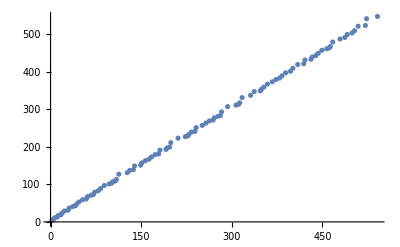

```mathematica
ListPlot@Map[({Prime[#],Prime[#+1]})&,Range[100]]
```

### 6-4. Create an anonymous function that takes three inputs and outputs one list with all three inputs in reverse order. (So for inputs 1, 4, 10, the output would be {10,4,1}.)

```mathematica
({#3,#2,#1})&[1,4,10]
```

{10,4,1}

```mathematica
(Reverse@{#1,#2,#3})&[1,4,10]
```

{10,4,1}

### 6-5. Before evaluating the following lines of code, anticipate what will be the result will be. After evaluating the code, understand why the output is what it is and compare it with your expectations. If there was an error, figure out what needs to be done to correct it.

```mathematica
Map[#[[2]]&,{{1,2},{3,4},{5,6},{7,8},{9,10}}]
```

```mathematica
Map[{#,#^2},Range[1,9,2]]
```

```mathematica
Map[Plot[x^#,{x,0,5}]&,{2,5,7}]
```

```mathematica
MapThread[#1^#2&,{Range[5],Range[5]}]
```

```mathematica
xlist={12,11,10,9}; 
ylist={1,2,3,4,5};
MapThread[(#1-#2)&,{xlist,ylist}]
```

```mathematica
alist=Range[0,Pi,Pi/6];
blist=Range[0,2Pi,Pi/3];
MapThread[Sin[#1]Cos[#2]&,alist,blist]
```

### 6-6. Use the function you created for Question 6-3 above to create a list of the coordinate pairs of {prime #n, prime #(n+1)} for n from 1 to 20. Then display these coordinate pairs as a connected scatterplot.

### 6-7. Use Map and Append to change the following coordinate pairs into coordinate triples by putting a zero into the third coordinate.

```mathematica
coords2D={{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}
```

## Challenge Questions

### 6-X1. Create an anonymous function that takes in two inputs, (think: a function and a number) and then applies the first input to the second (think: it applies the inputted function to the inputted number)

### 6-X2. Use LetterNumber to find the sum of the numerical values of the letters in your name. You will probably also need the command Characters.

```mathematica
Total[LetterNumber[Characters["Joshua Palter"]]]
```

146

### 6-X3. Create a function that takes as input a string and finds the sum of the numerical values of the letters in the string. (Similar to 6-X2 above.) Then use WordData and Histogram to find the distribution of these sums over words in the English Language.

### 6-X4. Consider the function that takes in a list and outputs a new list that consists of the reverse of the list with one more element at the end: the length of the original list. Create three copies this function that all do the same thing. Create one named function, create one function using the Function command, and create one unnamed function.

### 6-X5. When you finish: choose one of your recent comprehension questions that was difficult and discuss how you approached it.

```mathematica
colors=Table[Hue[x+RandomReal[0.1]],{x,0,0.9,.1}]
```

{Hue[0.004695154194191836],Hue[0.10893194505489852],Hue[0.2624010607296441],Hue[0.362642439211446],Hue[0.43929864858861717],Hue[0.5172596289319913],Hue[0.6635178956415692],Hue[0.7433047298212944],Hue[0.8683284789536898],Hue[0.9945990309932276]}

```mathematica
coords=Table[{i,i^2},{i,0,0.9,.1}]
```

{{0.,0.},{0.1,0.01},{0.2,0.04},{0.3,0.09},{0.4,0.16},{0.5,0.25},{0.6,0.36},{0.7,0.49},{0.8,0.64},{0.9,0.81}}

```mathematica
radii=RandomReal[{0.05,0.2},10]
```

{0.177949,0.0685471,0.106198,0.160217,0.152645,0.169102,0.109343,0.0883238,0.143515,0.0654073}

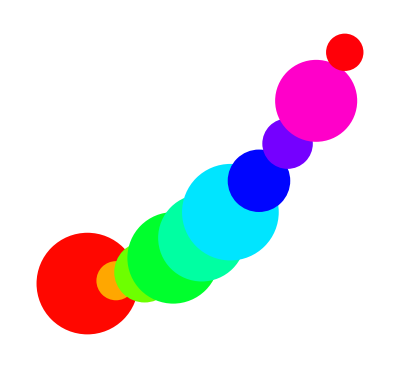

```mathematica
Graphics@MapThread[{#1,Disk[#2,#3]}&,{colors,coords,radii}]
```